## Глава 2. Представление рядов в системах компьютерной математики.

## §1. Числовые ряды

### 1.1. Сходимость ряда. Абсолютная и условная сходимость. Признаки абсолютной сходимости.

Пусть имеется числовой ряд:

u_1+u_2+...+u_n+...=∑_(n=1)^∞ u_n

К р и т е р и й  К о ш и. Для того чтобы числовой ряд (1) был сходящимся, необходимо и достаточно, чтобы для любого ϵ>0 , существовало N=N(ϵ) такое, что для всех n>N и p=1,2.... выполнялось неравенство

|S_(n+p)-S_n|=|u_(n+1)+u_(n+2)+...+u_(n+p)|<ϵ

Н е о б х о д и м ы й  п р и з н а к   с х о д и м о с т и.  Если ряд (1) сходится, то

lim_(n→∞) u_n=0

Ряд (1) называется абсолютно сходящимся, если сходится ряд из модулей членов этого ряда, т.е. сходится ряд

|u_1|+|u_2|+...+|u_n|+...=∑_(n=1)^∞ |u_n|

Если ряд (1) сходится, а ряд (3) расходится, то ряд (1) называется условно сходящимся.

П р и з н а к  с р а в н е н и я  р я д о в. Если члены ряда (1) для всех n>N_0 удовлетворяют условию |u_n|≤ b_n, причем ряд ∑_(n=1)^∞ b_n  сходится, то ряд (1) сходится абсолютно. Если же для n>N_1 члены ряда (1) удовлетворяют условию 0≤ c_n≤ |u_n|, причем ряд ∑_(n=1)^∞ с_n расходится, то ряд (1) не сходится абсолютно.

П р е д е л ь н ы й  п р и з н а к  с р а в н е н и я.  Если ряд ∑_(n=1)^∞ b_n  сходится абсолютно и существует конечный предел lim_(n→∞) |u_n/b_n|=q<+∞, то ряд (1) также сходится абсолютно. Если же члены рядов u_n и b_n - действительные положительные числа и

0<lim_(n→∞) u_n/b_n<+∞

то ряды ∑_(n=1)^∞ u_n и  ∑_(n=1)^∞ b_n либо оба сходятся, либо оба расходятся.

П р и з н а к  Д а л а м б е р а. Если члены ряда (1) таковы, что существует конечный предел

lim_(n→∞) |(u_(n+1))/u_n|=q

то при 0≤ q<1 ряд (1) сходится абсолютно, при q>1 - расходится, а при q=1 требуется дополнительное исследование.

П р и з н а к  К о ш и. Пусть

lim_(n→∞) (|u_n|)^(1/n)=q

Тогда при 0≤ q<1 ряд (1) сходится абсолютно, при q>1  (1) - расходится, а при q=1 требуется дополнительное исследование .

И н т е г р а л ь н ы й  п р и з н а к  К о ш и. Пусть функция f(x) положительна и монотонна при x≥ 1, и пусть для всех n∈ℕ имеет равенство f(n)=|u_n|. Тогда числовой ряд (3) сходится абсолютно или расходится с несобственным интегралом:

∫_a^∞ f(x)ⅆx, a≥ 1

##### Пример №12.24

Используя признак сравнения или предельный признак сравнения, исследовать на сходимость следующий ряд:

∑_(n=1)^∞ (n^2+3)/(4 n^3+5n)

Так как ряд ∑1/n расходится, и:

```mathematica
Limit[(n^2+3)/(4 n^3+5n)/(1/n), n-> Infinity]
```

1/4

Значит, по предельному признаку сравнения исходный ряд также расходится.

##### Пример №12.33

Пользуясь признаком Даламбера, исследовать на сходимость следующий ряд:

3/1+(3·5)/(1·4)+...+(3·5·...(2n+1))/(1·4·...(3n-2))

Запишем n-ый член ряда с помощью функции Product[f,{i,i_max}], которая в традиционном виде выглядит как: ∏_(i=1)^i_max f(i)

```mathematica
u[n_]:=Product[2k+1,{k,n}]/Product[3k-2,{k,n}]
```

Для определения абсолютной сходимости ряда воспользуемся признаком Даламбера (4):

```mathematica
Limit[Abs[u[n+1]/u[n]],n-> Infinity]//N
```

0.666667

Так как 0≤ 0.67< 1, то данный ряд сходится.

##### Пример №12.45

Используя признак Коши, исследовать на сходимость следующий ряд:

∑_(n=1)^∞ n (arcsin 1/n)^n

Запишем член ряда:

```mathematica
u[n_]:=n ( ArcSin[1/n])^n
```

Воспользуемся признаком Коши (5):

```mathematica
Limit[ (n ArcSin[1/n]^n)^(1/n),n-> Infinity]
```

0

По признаку Коши ряд сходится.

##### Пример № 12.52

Используя интегральный признак Коши, исследовать на сходимость следующие ряды:

∑_(n=3)^∞ 1/(n ln n (ln ln n)^2)

Запишем член ряда:

```mathematica
u[n_]:= (n Log[n] ( Log[Log[n]] )^2 )^-1
```

Воспользуемся интегральным признаком Коши (6):

```mathematica
Integrate[u[x],{x,3,Infinity}]
```

1/Log[Log[3]]

Получили, что данный интеграл сходится, значит и исходный ряд также сходится.

Система Wolfram Mathematica имеет встроенную функцию проверки сходимости ряда: SumConvergence[f,n]. Продемонстрируем его работу:

```mathematica
SumConvergence[1/n,n]
```

False

```mathematica
SumConvergence[1/(n Log[n] Log[Log[n]]^3),n]
```

```mathematica
True
```

```mathematica
SumConvergence[(2^(n^2))/(n!),n]
```

False

```mathematica
SumConvergence[1/(√n)Log[(n+1)/(n-1)],n]
```

True

В методических целях будем применять критерии сходимости, изложенные в теоретической части, а использовать функцию SumConvergence[f,n] будем для самопроверки.

Задания под номерами №№12.19-12.86 рекомендуются к самостоятельному решению.

### 1.2. Признаки условной сходимости.

П р и з н а к  Л е й б н и ц а. Пусть члены a_n знакочередующегося ряда

a_1-a_2+a_3+...+(-1)^(n+1)a_n+...

действительны и монотонно убывают, т.е.

a_1>a_2>a_3>....>a_n

и

lim_(n→∞) a_n=0

Тогда ряд (7) сходится, причем для его суммы S имеет место оценка S<a_1

П р и з н а к  А б е л я - Д и р и х л е. Пусть члены последовательности (b_n) монотонно убывают: b_1>b_2>b_3...>b_n,  и lim_(n→∞) b_n=0, а частичные суммы S_n=a_1+a_2+...+a_n, ограничены в совокупности, т.е.

|∑_(k=1)^n a_k|≤ M

тогда ряд ∑_(n=1)^∞ a_n b_n сходится.

##### Пример №12.95

Исследовать на абсолютную и условную сходимость следующий ряд:

∑_(n=2)^∞ (-1)^n(ln n)/n

Запишем член ряда:

```mathematica
a[n_]:=(-1)^n Log[n]/n
```

Исследуем на абсолютную сходимость ряд при помощи интегрального признака Коши:

```mathematica
Integrate[Abs[a[x]],{x,2,Infinity}]
```

Integrate::idiv: Integral of Log[x]/x does not converge on {2,∞}.

∫_2^∞ ⅇ^(-π Im[x]) Abs[Log[x]/x]ⅆx

Получили сообщение о том, что интеграл расходится.

Так как ряд не сходится абсолютно, исследуем на условную сходимость по признаку Лейбница.

Покажем графически, что модули членов ряда убывают:

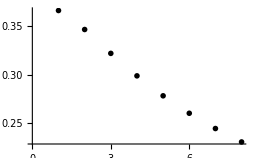

```mathematica
ListPlot[Table[Abs[a[n]],{n,3,10}]]
```

Первое условие признака Лейбница выполняется.

Найдем предел:

```mathematica
Limit[Abs[a[n]],n-> Infinity]
```

0

Условия признака Лейбница выполняются, следовательно ряд сходится условно. Проверим результат:

```mathematica
SumConvergence[Abs[a[n]],n]
```

False

```mathematica
SumConvergence[a[n],n]
```

True

Ответ: ряд сходится условно.

Данный порядок действий следует применить для решения задач под номерами №№12.90-12.109